```mathematica
CalcDiff[ca_,k_]:=Module[{difftable, initable, ftable, t},
	t = Length[ca];
	initable = ca[[1;;t-k]];
	ftable = ca[[k;;t]];
	difftable = Abs[ca[[#+k]]-ca[[#]]]& /@ Range[t-k]
	
	]
	
CreateTable[calist_]:=Module[{dtable,k,t},
	t = Length[calist[[1]]];
	Print[t]
	dtable = Table[CalcDiff[ca,#]&/@Range[4], {ca,calist}]
	]
```

```mathematica
c = CellularAutomaton[#,RandomInteger[1,50],{50,All}]& /@ Range[255];
```

```mathematica
d30 = CreateTable[c]
```

51

Set::write: Tag Times in dtable$101572 Null is Protected.

{{1},253,{{{1,0,0,1,0,0,0,0,1,1,0,1,0,0,0,1,1,1,0,0,0,0,1,0,0,0,1,1,1,1,1,0,1,1,1,0,1,0,1,1,0,1,0,1,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},43,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{1},{1},{1}}}
 |  |  |  |

```mathematica
d30
```

1
 |  |  |  |

```mathematica
d30[[1]]
```

{{{1,1,0,0,1,0,0,1,1,0,1,1,1,1,0,1,1,1,0,1,1,1,1,0,1,0,0,1,1,1,0,1,0,1,1,1,1,0,0,1,1,1,1,0,1,0,1,0,0,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},47,{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{1},48,{}}
 |  |  |  |

```mathematica
Dimensions[d30[[1]][[50]]]
```

{48,50}

```mathematica
Table[{i,ArrayPlot[d30[[i]][[#]]]&/@Range[4]},{i,Range[Length[c]]}]
```

{{1,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{2,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{3,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{4,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{5,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{6,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{7,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{8,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{9,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{10,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{11,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{12,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{13,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{14,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{15,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{16,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{17,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{18,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{19,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{20,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{21,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{22,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{23,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{24,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{25,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{26,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{27,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{28,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{29,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{30,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{31,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{32,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{33,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{34,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{35,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{36,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{37,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{38,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{39,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{40,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{41,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{42,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{43,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{44,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{45,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{46,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{47,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{48,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{49,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{50,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{51,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{52,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{53,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{54,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{55,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{56,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{57,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{58,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{59,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{60,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{61,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{62,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{63,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{64,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{65,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{66,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{67,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{68,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{69,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{70,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{71,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{72,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{73,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{74,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{75,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{76,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{77,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{78,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{79,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{80,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{81,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{82,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{83,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{84,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{85,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{86,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{87,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{88,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{89,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{90,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{91,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{92,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{93,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{94,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{95,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{96,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{97,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{98,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{99,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{100,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{101,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{102,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{103,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{104,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{105,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{106,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{107,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{108,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{109,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{110,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{111,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{112,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{113,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{114,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{115,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{116,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{117,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{118,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{119,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{120,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{121,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{122,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{123,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{124,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{125,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{126,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{127,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{128,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{129,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{130,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{131,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{132,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{133,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{134,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{135,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{136,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{137,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{138,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{139,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{140,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{141,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{142,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{143,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{144,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{145,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{146,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{147,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{148,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{149,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{150,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{151,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{152,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{153,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{154,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{155,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{156,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{157,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{158,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{159,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{160,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{161,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{162,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{163,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{164,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{165,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{166,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{167,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{168,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{169,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{170,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{171,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{172,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{173,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{174,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{175,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{176,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{177,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{178,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{179,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{180,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{181,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{182,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{183,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{184,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{185,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{186,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{187,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{188,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{189,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{190,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{191,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{192,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{193,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{194,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{195,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{196,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{197,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{198,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{199,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{200,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{201,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{202,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{203,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{204,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{205,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{206,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{207,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{208,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{209,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{210,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{211,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{212,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{213,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{214,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{215,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{216,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{217,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{218,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{219,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{220,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{221,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{222,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{223,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{224,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{225,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{226,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{227,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{228,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{229,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{230,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{231,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{232,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{233,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{234,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{235,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{236,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{237,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{238,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{239,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{240,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{241,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{242,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{243,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{244,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{245,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{246,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{247,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{248,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{249,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{250,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{251,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{252,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{253,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{254,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{255,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}}

```mathematica
c[[1]]
```

{1,0,0,1,1,0,0,0,1,1,0,0,0,0,0,1,0,0,0,1,0,1,0,1,0,1,1,0,0,0,0,1,0,0,1,0,0,1,1,1,1,0,1,1,1,1,0,0,1,0}

```mathematica
c[[1]] - c[[2]]
```

{0,-1,-1,0,1,-1,0,-1,0,1,-1,0,0,0,-1,0,-1,0,-1,0,0,0,0,0,0,0,1,-1,0,0,-1,0,-1,-1,0,-1,-1,0,1,1,1,0,0,1,1,1,-1,-1,0,0}

```mathematica
ca[[2;;50]]
```

Part::take: Cannot take positions 2 through 50 in ca.

ca⟦2;;50⟧

```mathematica
CalcDiff[c,2]
```

{{0,1,1,1,0,1,0,0,1,1,0,1,0,0,0,0,1,1,1,0,0,1,1,1,1,1,1,0,0,1,0,1,0,1,1,0,0,1,0,1,0,1,1,1,1,0,1,1,1,0},{1,1,1,0,0,1,1,1,0,0,0,1,1,0,0,1,1,1,0,1,0,0,0,0,0,1,1,1,0,1,0,0,1,0,1,1,0,0,1,1,0,1,1,0,0,0,1,1,0,1},{0,1,1,1,0,1,1,1,1,0,0,1,0,1,1,1,1,1,1,0,1,0,0,0,1,1,1,0,0,0,1,0,1,0,0,0,1,1,0,1,1,0,1,1,0,1,0,1,1,1},{0,1,1,0,0,1,0,1,0,1,1,1,0,1,0,1,0,1,0,0,1,1,0,0,1,1,1,1,0,0,1,0,1,1,0,0,0,1,1,0,0,0,0,1,1,0,1,0,0,0},{1,0,1,1,0,1,0,0,1,1,0,1,1,1,0,0,1,0,1,0,0,1,1,1,1,0,1,0,1,1,0,1,0,1,1,0,1,0,0,1,0,0,0,0,0,0,1,1,0,0},{0,1,0,0,0,0,1,0,1,0,0,1,1,1,1,0,1,0,1,1,1,0,0,1,0,0,0,1,1,1,1,1,0,0,1,1,0,1,0,0,1,0,0,0,0,0,0,1,1,0},{1,1,1,0,0,0,1,0,1,1,1,0,0,1,0,0,0,1,1,1,1,1,0,0,1,0,0,1,0,0,1,0,1,0,0,0,0,1,1,1,1,1,0,0,0,0,1,0,0,1},{0,1,1,1,0,1,0,1,1,1,1,1,0,0,1,0,0,1,0,0,1,0,1,1,1,1,1,1,1,1,0,1,0,1,0,0,0,1,0,0,1,1,1,0,0,0,0,1,0,1},{0,1,1,1,1,0,1,1,0,0,1,0,1,1,1,1,1,1,1,1,0,1,1,0,0,0,0,0,0,1,1,1,0,1,1,0,1,1,1,1,1,1,0,1,0,0,1,1,0,1},{0,0,0,1,0,0,0,0,1,1,0,1,1,0,0,0,0,0,0,1,1,1,0,1,0,0,0,0,1,1,1,1,1,0,1,1,0,0,0,0,1,1,1,0,1,0,1,1,1,1},{1,0,0,0,1,0,0,0,1,1,1,1,0,1,0,0,0,0,1,1,1,0,0,1,1,0,0,1,1,1,0,1,0,0,0,0,1,0,0,1,1,1,0,0,1,0,1,0,1,0},{0,1,0,1,1,1,0,1,1,0,1,0,0,1,1,0,0,1,1,1,1,1,0,1,0,1,1,1,1,1,1,0,1,0,0,0,0,1,0,1,1,1,1,0,0,1,1,0,0,1},{0,0,1,1,1,1,1,0,0,0,0,1,0,1,0,1,1,1,1,0,1,0,0,1,0,1,0,1,0,1,0,0,1,1,0,0,1,1,0,1,0,1,0,1,1,0,1,1,0,1},{1,0,1,0,0,1,0,1,0,0,0,1,0,1,0,1,0,1,1,1,0,1,0,0,1,1,0,0,1,0,1,0,0,1,1,0,1,1,1,1,0,0,1,0,1,1,0,0,0,0},{1,0,1,1,1,0,1,0,1,0,1,0,1,0,1,1,0,1,1,0,0,1,1,1,0,1,1,0,1,0,1,1,1,0,0,0,1,0,1,1,1,0,1,0,0,0,1,0,0,0},{0,1,1,0,1,1,1,0,0,1,0,1,1,0,0,1,1,0,1,1,0,1,1,1,1,0,0,0,0,1,1,1,1,1,0,0,1,0,1,1,0,0,1,1,0,0,0,1,0,1},{1,1,0,0,1,1,1,1,0,1,0,0,0,1,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,1,0,0,1,0,1,1,0,1,0,1,1,0,0,1,1,0,1,0,1,0},{0,0,1,1,0,0,1,0,0,1,1,0,0,0,1,0,0,0,0,0,0,1,0,0,1,0,1,0,1,1,1,1,0,1,1,1,1,1,0,0,0,1,1,0,1,1,0,1,1,0},{0,0,0,1,1,0,0,1,0,0,1,1,0,1,1,1,0,0,0,0,1,0,1,0,1,0,0,1,1,0,0,1,1,1,0,0,1,0,1,0,0,0,1,1,0,0,0,0,0,1},{1,0,1,0,0,1,1,1,1,1,0,1,1,1,1,1,1,0,0,0,0,1,1,0,0,1,0,1,0,1,1,1,1,0,1,1,0,1,0,1,0,1,0,0,1,0,0,0,0,0},{0,1,0,1,0,1,0,0,1,1,1,0,0,0,0,1,0,1,0,0,1,0,1,1,0,1,0,1,0,1,0,1,1,1,1,1,1,1,0,0,1,0,1,0,0,1,0,0,0,1},{1,1,0,1,0,1,1,1,1,1,0,1,0,0,1,0,1,0,1,0,0,1,0,0,0,0,1,0,1,1,0,1,1,0,0,0,1,1,1,0,1,0,1,1,1,1,1,0,0,0},{0,1,1,0,1,1,0,0,1,1,1,0,1,0,0,1,1,0,1,1,1,1,1,0,0,0,1,0,0,1,1,0,1,1,0,1,1,1,0,0,0,1,1,0,0,1,1,1,0,1},{1,0,0,0,0,0,1,1,1,1,0,0,1,1,1,0,1,1,1,0,0,1,1,1,0,1,1,1,0,0,0,0,0,1,1,1,1,1,1,0,0,1,0,1,1,1,1,1,1,0},{1,1,0,0,0,0,1,0,1,1,1,0,1,1,1,1,0,0,0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,1,0,1,1,1,0,1,0,1,0,1,0,0},{0,1,1,0,0,1,1,0,1,1,0,0,1,0,1,0,1,0,1,1,0,1,0,1,0,0,0,1,0,1,0,0,0,0,0,0,1,0,1,1,0,1,1,1,0,0,1,0,1,0},{1,0,0,1,0,0,0,0,0,1,1,0,1,0,0,1,0,1,0,0,0,0,1,0,1,0,1,0,1,0,1,0,0,0,0,0,0,1,1,0,0,1,1,1,1,0,1,0,1,1},{1,1,0,0,1,0,0,0,0,0,0,0,0,1,0,1,0,1,1,0,0,0,1,0,0,1,0,1,1,0,1,1,0,0,0,0,1,0,0,1,1,0,0,1,0,0,0,1,1,1},{1,0,1,1,1,1,0,0,0,0,0,0,0,1,0,0,1,0,1,1,0,1,0,1,0,1,0,0,1,1,0,1,1,0,0,0,0,1,0,0,1,1,0,0,1,0,0,1,0,0},{0,1,1,0,1,1,1,0,0,0,0,0,1,0,1,0,1,0,0,1,1,0,1,1,0,1,1,0,0,0,0,0,0,1,0,0,1,1,1,1,0,0,1,1,1,1,1,1,1,1},{1,1,0,0,1,1,0,1,0,0,0,0,0,1,1,0,1,1,0,0,0,0,0,1,1,0,1,1,0,0,0,0,0,0,1,0,1,0,1,1,1,0,1,0,0,0,0,0,0,1},{1,0,1,1,0,1,1,0,1,0,0,0,1,0,1,1,0,1,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,1,1,0,0,1,1,0,0,0,0,1,1},{1,1,0,1,1,0,0,0,1,1,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,1,1,1,1,0,0,1,1,0,1,0,1,0,0,1,1,1},{1,0,0,0,0,1,0,0,0,1,1,0,1,1,1,0,0,0,0,0,1,0,0,0,0,0,0,0,1,1,1,0,1,1,0,1,0,1,0,0,0,0,1,0,1,1,1,1,1,0},{0,1,0,0,0,0,1,0,1,0,1,1,1,1,1,1,0,0,0,1,1,1,0,0,0,0,0,0,1,1,1,1,0,0,0,0,1,0,1,0,0,0,0,1,1,0,0,1,1,1},{0,1,1,0,0,1,0,1,0,1,0,0,0,0,1,0,1,0,0,1,1,1,1,0,0,0,0,1,1,0,1,0,1,0,0,0,1,0,1,1,0,0,1,0,0,1,1,1,1,0},{0,0,1,1,0,0,1,1,0,1,1,0,0,1,0,1,0,1,1,1,0,1,0,1,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0,1,1,0,0,1,0,1,0,1,1,1},{1,1,0,0,1,1,0,1,1,0,1,1,0,0,1,1,0,1,1,0,0,0,1,0,1,0,0,0,0,0,0,1,0,0,1,0,1,1,0,0,0,1,1,1,0,1,0,1,1,0},{0,1,1,0,0,1,1,0,0,0,0,0,1,1,0,1,1,0,1,1,0,0,1,0,1,1,0,0,0,0,1,0,1,0,1,0,0,0,1,0,0,1,0,1,1,1,0,0,1,1},{0,0,0,1,1,0,0,1,0,0,0,0,0,1,1,0,0,0,0,0,1,1,0,1,0,1,1,0,0,0,0,1,1,0,1,1,0,0,0,1,1,1,0,1,1,0,1,0,0,0},{0,0,0,0,1,1,0,0,1,0,0,0,1,0,0,1,0,0,0,0,1,1,1,1,0,0,0,1,0,0,1,0,1,1,0,1,1,0,1,1,1,0,0,0,1,1,0,1,0,0},{0,0,0,1,0,0,1,1,1,1,0,0,0,1,0,0,1,0,0,1,1,0,1,0,1,0,0,0,1,0,0,1,0,0,0,0,1,1,1,1,1,1,0,0,0,0,0,1,1,0},{0,0,0,0,1,0,1,0,1,1,1,0,1,1,1,1,1,1,0,0,0,0,0,1,0,1,0,1,1,1,1,1,1,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,1,1},{1,0,0,1,1,0,1,0,1,1,1,1,1,0,0,0,1,1,1,0,0,0,0,1,0,0,1,1,0,0,0,1,1,1,0,0,0,0,0,1,0,1,0,1,0,0,0,1,0,0},{0,1,0,1,1,1,1,0,0,0,1,0,0,1,0,1,1,1,0,1,0,0,1,0,1,0,1,0,1,0,1,1,1,0,1,0,0,0,0,0,1,1,0,1,1,0,0,0,1,0},{1,1,0,1,0,1,0,1,0,0,0,1,1,1,0,1,1,1,1,0,1,0,0,1,1,0,1,0,1,0,1,1,1,1,0,1,0,0,0,1,0,1,1,0,1,1,0,1,1,1},{0,1,1,1,0,0,1,0,1,0,1,1,1,0,0,0,0,1,0,0,1,1,1,0,1,1,0,1,1,0,0,0,1,0,0,1,1,0,0,0,1,0,0,0,0,1,1,1,0,0},{1,1,1,1,1,0,1,0,0,1,1,1,1,1,0,0,0,0,1,0,1,1,1,1,0,0,0,0,0,1,0,0,0,1,0,0,1,1,0,1,1,1,0,0,0,0,0,0,1,0},{1,1,0,1,0,0,0,1,0,1,0,0,1,0,1,0,0,1,1,0,1,0,1,0,1,0,0,0,0,0,1,0,1,1,1,1,0,1,1,1,1,1,1,0,0,0,0,1,1,0}}

```mathematica
Length[d]
```

49

```mathematica
Abs[-1]
```

1

{1,2,3,Abs[Null],1}

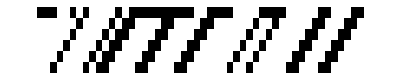
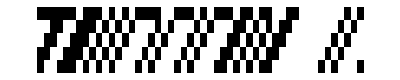
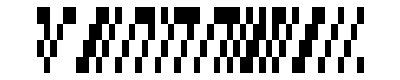
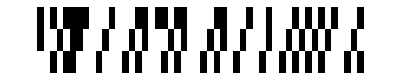
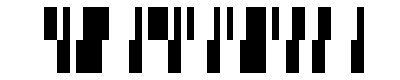
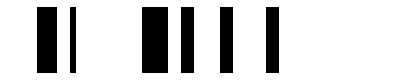
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Abs[{1,2,3,,-1}]
```